```mathematica
Clear["Global`*"];
Quit[];
```

# MF superconductor: diagonalization and GS iteration

```mathematica
<<sneg`sneg`;
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

Starts with the MF approximation of the superconducting Hamiltonian (where neighbouring levels do not interact). H is 
diagonalized in Nambu basis. 
In the second part, the operators are applied to their vacuum (0101...01), in order to obtain a ground state. 
In the third part, energy and occupancy number are calculated.

```mathematica
(*Physical parameters*)
n=6; (* number of levels *)
W=1.; (* band [-W:W] *)
ρ=n/(2W); (* density of states *)
spacing=2W/(n+1); (*spacing between energy levels*)
ϵ[i_]:=-W+(2W)/(n+1)i; (* energy levels *)
μ=0; (* chemical potential *)
Δ=0.1; (* initial approximation for Δ. True Δ is determined self-consistently. *)
B=0; (* magnetic field *)
g=0.5/ρ; (* Coupling constant. Note that we keep g*ρ constant, since this combination enters the BCS expression for Δ. *)
h[i_, Δ_]:={{ϵ[i]-μ+B,Δ},{Δ,-(ϵ[i]-μ)+B}}; (* Hamiltonian block *)
dim=2; (* Dimension of the block *)
zm2=DiagonalMatrix[{0,0}]; (* zero dimxdim matrix *)
matrix[Δ_]:=ArrayFlatten[Table[If[i==j,h[i, Δ],zm2],{i,n},{j,n}]];(* MF Hamiltonian *)
```

```mathematica
Table[ϵ[i],{i, n}]
```

{-0.5,0.,0.5}

```mathematica
matrix[0.1]//MatrixForm
```

(-0.5 | 0.1 | 0 | 0 | 0 | 0
0.1 | 0.5 | 0 | 0 | 0 | 0
0 | 0 | 0. | 0.1 | 0 | 0
0 | 0 | 0.1 | 0. | 0 | 0
0 | 0 | 0 | 0 | 0.5 | 0.1
0 | 0 | 0 | 0 | 0.1 | -0.5)

## Diagonalization

```mathematica
(*Computing parameters used in the while loop*)
precision = 0.000001;
maxIteration=20;
iteration = 0;
oldΔ = Δ+1;
```

```mathematica
(* j: state number *)
(* i: level index *)
u[j_,i_]:=vectors[[j,dim(i-1)+1]]
v[j_,i_]:=vectors[[j,dim(i-1)+2]]
```

```mathematica
(*The loop calculates Δ self-consistently*)
While[Abs[(Δ/oldΔ)-1]>precision ∧ iteration<maxIteration,
{energies, vectors} =Transpose[Sort[Transpose[Eigensystem[matrix[Δ]]]]];
oldΔ=Δ;
Δ= Sum[-g u[j,i]v[j,i],{j,n},{i,n}];
iteration++;
]
```

```mathematica
iteration
```

19

```mathematica
Δ//FullForm
```

0.320084

```mathematica
energies
```

{-0.782724,-0.782724,-0.534908,-0.534908,-0.350516,-0.350516,0.350516,0.350516,0.534908,0.534908,0.782724,0.782724}

```mathematica
Table[u[j,i],{j,n},{i,n}]//MatrixForm
```

(0.977897 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.209089
0. | 0.949001 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.315273 | 0.
0. | 0. | 0.838917 | 0. | 0. | 0.
0. | 0. | 0. | 0.54426 | 0. | 0.)

```mathematica
Table[v[j,i],{j,n},{i,n}]//MatrixForm
```

(-0.209089 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.977897
0. | -0.315273 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.949001 | 0.
0. | 0. | -0.54426 | 0. | 0. | 0.
0. | 0. | 0. | -0.838917 | 0. | 0.)

## GS iteration

```mathematica
Off[General::spell1];
snegfermionoperators[c]
snegrealconstants[t,U]
```

```mathematica
mybasis = makebasis[Table[c[i],{i, n}]];
```

```mathematica
(*Exact Hamiltonian*)
kinetic=Sum[ϵ[j](nc[c[CR,j,UP ],c[AN,j,UP]]+nc[c[CR,j,DO],c[AN,j,DO]]),{j,n}];
interaction=-g Sum[ nc[nc[c[CR,j,UP],c[CR,j,DO]],nc[c[AN,i,UP],c[AN,i,DO]]],{j,n}, {i, n}]
Hexact = kinetic+interaction;
```

-0.166667 (c_(1↓)^†·c_(1⇑)^†·c_(1↓)^·c_(1⇑)^+c_(1↓)^†·c_(1⇑)^†·c_(2↓)^·c_(2⇑)^+c_(1↓)^†·c_(1⇑)^†·c_(3↓)^·c_(3⇑)^+c_(1↓)^†·c_(1⇑)^†·c_(4↓)^·c_(4⇑)^+c_(1↓)^†·c_(1⇑)^†·c_(5↓)^·c_(5⇑)^+c_(1↓)^†·c_(1⇑)^†·c_(6↓)^·c_(6⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(1↓)^·c_(1⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(2↓)^·c_(2⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(3↓)^·c_(3⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(4↓)^·c_(4⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(5↓)^·c_(5⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(6↓)^·c_(6⇑)^+c_(3↓)^†·c_(3⇑)^†·c_(1↓)^·c_(1⇑)^+c_(3↓)^†·c_(3⇑)^†·c_(2↓)^·c_(2⇑)^+c_(3↓)^†·c_(3⇑)^†·c_(3↓)^·c_(3⇑)^+c_(3↓)^†·c_(3⇑)^†·c_(4↓)^·c_(4⇑)^+c_(3↓)^†·c_(3⇑)^†·c_(5↓)^·c_(5⇑)^+c_(3↓)^†·c_(3⇑)^†·c_(6↓)^·c_(6⇑)^+c_(4↓)^†·c_(4⇑)^†·c_(1↓)^·c_(1⇑)^+c_(4↓)^†·c_(4⇑)^†·c_(2↓)^·c_(2⇑)^+c_(4↓)^†·c_(4⇑)^†·c_(3↓)^·c_(3⇑)^+c_(4↓)^†·c_(4⇑)^†·c_(4↓)^·c_(4⇑)^+c_(4↓)^†·c_(4⇑)^†·c_(5↓)^·c_(5⇑)^+c_(4↓)^†·c_(4⇑)^†·c_(6↓)^·c_(6⇑)^+c_(5↓)^†·c_(5⇑)^†·c_(1↓)^·c_(1⇑)^+c_(5↓)^†·c_(5⇑)^†·c_(2↓)^·c_(2⇑)^+c_(5↓)^†·c_(5⇑)^†·c_(3↓)^·c_(3⇑)^+c_(5↓)^†·c_(5⇑)^†·c_(4↓)^·c_(4⇑)^+c_(5↓)^†·c_(5⇑)^†·c_(5↓)^·c_(5⇑)^+c_(5↓)^†·c_(5⇑)^†·c_(6↓)^·c_(6⇑)^+c_(6↓)^†·c_(6⇑)^†·c_(1↓)^·c_(1⇑)^+c_(6↓)^†·c_(6⇑)^†·c_(2↓)^·c_(2⇑)^+c_(6↓)^†·c_(6⇑)^†·c_(3↓)^·c_(3⇑)^+c_(6↓)^†·c_(6⇑)^†·c_(4↓)^·c_(4⇑)^+c_(6↓)^†·c_(6⇑)^†·c_(5↓)^·c_(5⇑)^+c_(6↓)^†·c_(6⇑)^†·c_(6↓)^·c_(6⇑)^)

```mathematica
(*MF Hamiltonian*)
kinetic=Sum[ϵ[j](nc[c[CR,j,UP ],c[AN,j,UP]]+nc[c[CR,j,DO],c[AN,j,DO]]),{j,n}];
interactionMF= Sum[Δ nc[c[CR,j,UP],c[CR,j,DO]]+ conj[Δ]nc[c[AN,j,DO],c[AN,j,UP]],{j, n}]
HMF = kinetic+interactionMF+(Δ^2)/g;
```

-0.320084 c_(1↓)^†·c_(1⇑)^†-0.320084 c_(2↓)^†·c_(2⇑)^†-0.320084 c_(3↓)^†·c_(3⇑)^†-0.320084 c_(4↓)^†·c_(4⇑)^†-0.320084 c_(5↓)^†·c_(5⇑)^†-0.320084 c_(6↓)^†·c_(6⇑)^†+0.320084 c_(1↓)^·c_(1⇑)^+0.320084 c_(2↓)^·c_(2⇑)^+0.320084 c_(3↓)^·c_(3⇑)^+0.320084 c_(4↓)^·c_(4⇑)^+0.320084 c_(5↓)^·c_(5⇑)^+0.320084 c_(6↓)^·c_(6⇑)^

```mathematica
(*Initial state*)
V = vc@@Table[(1/2)(1+(-1)^i),{i, 2n}]
```

‖▯▮▯▮▯▮▯▮▯▮▯▮⟩

```mathematica
(*Diagonal operators*)
d[j_]:=Sum[u[j, i]c[CR,i,UP] + v[j, i]c[AN,i,DO],{i,n}]
```

```mathematica
(*Iteratively construct a list of successive states η. η[i]=d[i-1]d[i-1]...d[1].V*)
η={V};
Do[η=Append[η,ap[d[i],η[[-1]]]],{i, n}];
```

```mathematica
η[[-1]]//FullSimplify
```

0.+0.0279321‖▯▯▯▯▯▯▯▯▯▯▯▯⟩-0.0059723‖▯▯▯▯▯▯▯▯▯▯▮▮⟩-0.00927948‖▯▯▯▯▯▯▯▯▮▮▯▯⟩+0.00198409‖▯▯▯▯▯▯▯▯▮▮▮▮⟩-0.0181213‖▯▯▯▯▯▯▮▮▯▯▯▯⟩+0.00387462‖▯▯▯▯▯▯▮▮▯▯▮▮⟩+0.0060202‖▯▯▯▯▯▯▮▮▮▮▯▯⟩-0.00128721‖▯▯▯▯▯▯▮▮▮▮▮▮⟩-0.0430542‖▯▯▯▯▮▮▯▯▯▯▯▯⟩+0.00920564‖▯▯▯▯▮▮▯▯▯▯▮▮⟩+0.0143033‖▯▯▯▯▮▮▯▯▮▮▯▯⟩-0.00305826‖▯▯▯▯▮▮▯▯▮▮▮▮⟩+0.0279321‖▯▯▯▯▮▮▮▮▯▯▯▯⟩-0.0059723‖▯▯▯▯▮▮▮▮▯▯▮▮⟩-0.00927948‖▯▯▯▯▮▮▮▮▮▮▯▯⟩+0.00198409‖▯▯▯▯▮▮▮▮▮▮▮▮⟩-0.084078‖▯▯▮▮▯▯▯▯▯▯▯▯⟩+0.0179771‖▯▯▮▮▯▯▯▯▯▯▮▮⟩+0.0279321‖▯▯▮▮▯▯▯▯▮▮▯▯⟩-0.0059723‖▯▯▮▮▯▯▯▯▮▮▮▮⟩+0.0545469‖▯▯▮▮▯▯▮▮▯▯▯▯⟩-0.0116629‖▯▯▮▮▯▯▮▮▯▯▮▮⟩-0.0181213‖▯▯▮▮▯▯▮▮▮▮▯▯⟩+0.00387462‖▯▯▮▮▯▯▮▮▮▮▮▮⟩+0.129597‖▯▯▮▮▮▮▯▯▯▯▯▯⟩-0.0277098‖▯▯▮▮▮▮▯▯▯▯▮▮⟩-0.0430542‖▯▯▮▮▮▮▯▯▮▮▯▯⟩+0.00920564‖▯▯▮▮▮▮▯▯▮▮▮▮⟩-0.084078‖▯▯▮▮▮▮▮▮▯▯▯▯⟩+0.0179771‖▯▯▮▮▮▮▮▮▯▯▮▮⟩+0.0279321‖▯▯▮▮▮▮▮▮▮▮▯▯⟩-0.0059723‖▯▯▮▮▮▮▮▮▮▮▮▮⟩-0.130637‖▮▮▯▯▯▯▯▯▯▯▯▯⟩+0.0279321‖▮▮▯▯▯▯▯▯▯▯▮▮⟩+0.0433995‖▮▮▯▯▯▯▯▯▮▮▯▯⟩-0.00927948‖▮▮▯▯▯▯▯▯▮▮▮▮⟩+0.0847524‖▮▮▯▯▯▯▮▮▯▯▯▯⟩-0.0181213‖▮▮▯▯▯▯▮▮▯▯▮▮⟩-0.0281561‖▮▮▯▯▯▯▮▮▮▮▯▯⟩+0.0060202‖▮▮▯▯▯▯▮▮▮▮▮▮⟩+0.201362‖▮▮▯▯▮▮▯▯▯▯▯▯⟩-0.0430542‖▮▮▯▯▮▮▯▯▯▯▮▮⟩-0.0668956‖▮▮▯▯▮▮▯▯▮▮▯▯⟩+0.0143033‖▮▮▯▯▮▮▯▯▮▮▮▮⟩-0.130637‖▮▮▯▯▮▮▮▮▯▯▯▯⟩+0.0279321‖▮▮▯▯▮▮▮▮▯▯▮▮⟩+0.0433995‖▮▮▯▯▮▮▮▮▮▮▯▯⟩-0.00927948‖▮▮▯▯▮▮▮▮▮▮▮▮⟩+0.393228‖▮▮▮▮▯▯▯▯▯▯▯▯⟩-0.084078‖▮▮▮▮▯▯▯▯▯▯▮▮⟩-0.130637‖▮▮▮▮▯▯▯▯▮▮▯▯⟩+0.0279321‖▮▮▮▮▯▯▯▯▮▮▮▮⟩-0.255113‖▮▮▮▮▯▯▮▮▯▯▯▯⟩+0.0545469‖▮▮▮▮▯▯▮▮▯▯▮▮⟩+0.0847524‖▮▮▮▮▯▯▮▮▮▮▯▯⟩-0.0181213‖▮▮▮▮▯▯▮▮▮▮▮▮⟩-0.606118‖▮▮▮▮▮▮▯▯▯▯▯▯⟩+0.129597‖▮▮▮▮▮▮▯▯▯▯▮▮⟩+0.201362‖▮▮▮▮▮▮▯▯▮▮▯▯⟩-0.0430542‖▮▮▮▮▮▮▯▯▮▮▮▮⟩+0.393228‖▮▮▮▮▮▮▮▮▯▯▯▯⟩-0.084078‖▮▮▮▮▮▮▮▮▯▯▮▮⟩-0.130637‖▮▮▮▮▮▮▮▮▮▮▯▯⟩+0.0279321‖▮▮▮▮▮▮▮▮▮▮▮▮⟩

```mathematica
η//FullSimplify
```

{‖▯▮▯▮▯▮▯▮▯▮▯▮⟩,0.-0.209089‖▯▯▯▮▯▮▯▮▯▮▯▮⟩+0.977897‖▮▮▯▮▯▮▯▮▯▮▯▮⟩,0.-0.204467‖▯▯▯▮▯▮▯▮▯▮▯▯⟩+0.0437182‖▯▯▯▮▯▮▯▮▯▮▮▮⟩+0.956282‖▮▮▯▮▯▮▯▮▯▮▯▯⟩-0.204467‖▮▮▯▮▯▮▯▮▯▮▮▮⟩,0.+0.0644631‖▯▯▯▯▯▮▯▮▯▮▯▯⟩-0.0137832‖▯▯▯▯▯▮▯▮▯▮▮▮⟩-0.19404‖▯▯▮▮▯▮▯▮▯▮▯▯⟩+0.0414886‖▯▯▮▮▯▮▯▮▯▮▮▮⟩-0.30149‖▮▮▯▯▯▮▯▮▯▮▯▯⟩+0.0644631‖▮▮▯▯▯▮▯▮▯▮▮▮⟩+0.907512‖▮▮▮▮▯▮▯▮▯▮▯▯⟩-0.19404‖▮▮▮▮▯▮▯▮▯▮▮▮⟩,0.+0.0611755‖▯▯▯▯▯▮▯▮▯▯▯▯⟩-0.0130803‖▯▯▯▯▯▮▯▮▯▯▮▮⟩-0.0203235‖▯▯▯▯▯▮▯▮▮▮▯▯⟩+0.00434547‖▯▯▯▯▯▮▯▮▮▮▮▮⟩-0.184144‖▯▯▮▮▯▮▯▮▯▯▯▯⟩+0.0393727‖▯▯▮▮▯▮▯▮▯▯▮▮⟩+0.0611755‖▯▯▮▮▯▮▯▮▮▮▯▯⟩-0.0130803‖▯▯▮▮▯▮▯▮▮▮▮▮⟩-0.286114‖▮▮▯▯▯▮▯▮▯▯▯▯⟩+0.0611755‖▮▮▯▯▯▮▯▮▯▯▮▮⟩+0.0950517‖▮▮▯▯▯▮▯▮▮▮▯▯⟩-0.0203235‖▮▮▯▯▯▮▯▮▮▮▮▮⟩+0.86123‖▮▮▮▮▯▮▯▮▯▯▯▯⟩-0.184144‖▮▮▮▮▯▮▯▮▯▯▮▮⟩-0.286114‖▮▮▮▮▯▮▯▮▮▮▯▯⟩+0.0611755‖▮▮▮▮▯▮▯▮▮▮▮▮⟩,0.-0.0332954‖▯▯▯▯▯▯▯▮▯▯▯▯⟩+0.00711906‖▯▯▯▯▯▯▯▮▯▯▮▮⟩+0.0110613‖▯▯▯▯▯▯▯▮▮▮▯▯⟩-0.00236506‖▯▯▯▯▯▯▯▮▮▮▮▮⟩+0.0513212‖▯▯▯▯▮▮▯▮▯▯▯▯⟩-0.0109732‖▯▯▯▯▮▮▯▮▯▯▮▮⟩-0.0170497‖▯▯▯▯▮▮▯▮▮▮▯▯⟩+0.00364549‖▯▯▯▯▮▮▯▮▮▮▮▮⟩+0.100222‖▯▯▮▮▯▯▯▮▯▯▯▯⟩-0.021429‖▯▯▮▮▯▯▯▮▯▯▮▮⟩-0.0332954‖▯▯▮▮▯▯▯▮▮▮▯▯⟩+0.00711906‖▯▯▮▮▯▯▯▮▮▮▮▮⟩-0.154481‖▯▯▮▮▮▮▯▮▯▯▯▯⟩+0.0330305‖▯▯▮▮▮▮▯▮▯▯▮▮⟩+0.0513212‖▯▯▮▮▮▮▯▮▮▮▯▯⟩-0.0109732‖▯▯▮▮▮▮▯▮▮▮▮▮⟩+0.155721‖▮▮▯▯▯▯▯▮▯▯▯▯⟩-0.0332954‖▮▮▯▯▯▯▯▮▯▯▮▮⟩-0.0517328‖▮▮▯▯▯▯▯▮▮▮▯▯⟩+0.0110613‖▮▮▯▯▯▯▯▮▮▮▮▮⟩-0.240026‖▮▮▯▯▮▮▯▮▯▯▯▯⟩+0.0513212‖▮▮▯▯▮▮▯▮▯▯▮▮⟩+0.0797405‖▮▮▯▯▮▮▯▮▮▮▯▯⟩-0.0170497‖▮▮▯▯▮▮▯▮▮▮▮▮⟩-0.468733‖▮▮▮▮▯▯▯▮▯▯▯▯⟩+0.100222‖▮▮▮▮▯▯▯▮▯▯▮▮⟩+0.155721‖▮▮▮▮▯▯▯▮▮▮▯▯⟩-0.0332954‖▮▮▮▮▯▯▯▮▮▮▮▮⟩+0.7225‖▮▮▮▮▮▮▯▮▯▯▯▯⟩-0.154481‖▮▮▮▮▮▮▯▮▯▯▮▮⟩-0.240026‖▮▮▮▮▮▮▯▮▮▮▯▯⟩+0.0513212‖▮▮▮▮▮▮▯▮▮▮▮▮⟩,0.+0.0279321‖▯▯▯▯▯▯▯▯▯▯▯▯⟩-0.0059723‖▯▯▯▯▯▯▯▯▯▯▮▮⟩-0.00927948‖▯▯▯▯▯▯▯▯▮▮▯▯⟩+0.00198409‖▯▯▯▯▯▯▯▯▮▮▮▮⟩-0.0181213‖▯▯▯▯▯▯▮▮▯▯▯▯⟩+0.00387462‖▯▯▯▯▯▯▮▮▯▯▮▮⟩+0.0060202‖▯▯▯▯▯▯▮▮▮▮▯▯⟩-0.00128721‖▯▯▯▯▯▯▮▮▮▮▮▮⟩-0.0430542‖▯▯▯▯▮▮▯▯▯▯▯▯⟩+0.00920564‖▯▯▯▯▮▮▯▯▯▯▮▮⟩+0.0143033‖▯▯▯▯▮▮▯▯▮▮▯▯⟩-0.00305826‖▯▯▯▯▮▮▯▯▮▮▮▮⟩+0.0279321‖▯▯▯▯▮▮▮▮▯▯▯▯⟩-0.0059723‖▯▯▯▯▮▮▮▮▯▯▮▮⟩-0.00927948‖▯▯▯▯▮▮▮▮▮▮▯▯⟩+0.00198409‖▯▯▯▯▮▮▮▮▮▮▮▮⟩-0.084078‖▯▯▮▮▯▯▯▯▯▯▯▯⟩+0.0179771‖▯▯▮▮▯▯▯▯▯▯▮▮⟩+0.0279321‖▯▯▮▮▯▯▯▯▮▮▯▯⟩-0.0059723‖▯▯▮▮▯▯▯▯▮▮▮▮⟩+0.0545469‖▯▯▮▮▯▯▮▮▯▯▯▯⟩-0.0116629‖▯▯▮▮▯▯▮▮▯▯▮▮⟩-0.0181213‖▯▯▮▮▯▯▮▮▮▮▯▯⟩+0.00387462‖▯▯▮▮▯▯▮▮▮▮▮▮⟩+0.129597‖▯▯▮▮▮▮▯▯▯▯▯▯⟩-0.0277098‖▯▯▮▮▮▮▯▯▯▯▮▮⟩-0.0430542‖▯▯▮▮▮▮▯▯▮▮▯▯⟩+0.00920564‖▯▯▮▮▮▮▯▯▮▮▮▮⟩-0.084078‖▯▯▮▮▮▮▮▮▯▯▯▯⟩+0.0179771‖▯▯▮▮▮▮▮▮▯▯▮▮⟩+0.0279321‖▯▯▮▮▮▮▮▮▮▮▯▯⟩-0.0059723‖▯▯▮▮▮▮▮▮▮▮▮▮⟩-0.130637‖▮▮▯▯▯▯▯▯▯▯▯▯⟩+0.0279321‖▮▮▯▯▯▯▯▯▯▯▮▮⟩+0.0433995‖▮▮▯▯▯▯▯▯▮▮▯▯⟩-0.00927948‖▮▮▯▯▯▯▯▯▮▮▮▮⟩+0.0847524‖▮▮▯▯▯▯▮▮▯▯▯▯⟩-0.0181213‖▮▮▯▯▯▯▮▮▯▯▮▮⟩-0.0281561‖▮▮▯▯▯▯▮▮▮▮▯▯⟩+0.0060202‖▮▮▯▯▯▯▮▮▮▮▮▮⟩+0.201362‖▮▮▯▯▮▮▯▯▯▯▯▯⟩-0.0430542‖▮▮▯▯▮▮▯▯▯▯▮▮⟩-0.0668956‖▮▮▯▯▮▮▯▯▮▮▯▯⟩+0.0143033‖▮▮▯▯▮▮▯▯▮▮▮▮⟩-0.130637‖▮▮▯▯▮▮▮▮▯▯▯▯⟩+0.0279321‖▮▮▯▯▮▮▮▮▯▯▮▮⟩+0.0433995‖▮▮▯▯▮▮▮▮▮▮▯▯⟩-0.00927948‖▮▮▯▯▮▮▮▮▮▮▮▮⟩+0.393228‖▮▮▮▮▯▯▯▯▯▯▯▯⟩-0.084078‖▮▮▮▮▯▯▯▯▯▯▮▮⟩-0.130637‖▮▮▮▮▯▯▯▯▮▮▯▯⟩+0.0279321‖▮▮▮▮▯▯▯▯▮▮▮▮⟩-0.255113‖▮▮▮▮▯▯▮▮▯▯▯▯⟩+0.0545469‖▮▮▮▮▯▯▮▮▯▯▮▮⟩+0.0847524‖▮▮▮▮▯▯▮▮▮▮▯▯⟩-0.0181213‖▮▮▮▮▯▯▮▮▮▮▮▮⟩-0.606118‖▮▮▮▮▮▮▯▯▯▯▯▯⟩+0.129597‖▮▮▮▮▮▮▯▯▯▯▮▮⟩+0.201362‖▮▮▮▮▮▮▯▯▮▮▯▯⟩-0.0430542‖▮▮▮▮▮▮▯▯▮▮▮▮⟩+0.393228‖▮▮▮▮▮▮▮▮▯▯▯▯⟩-0.084078‖▮▮▮▮▮▮▮▮▯▯▮▮⟩-0.130637‖▮▮▮▮▮▮▮▮▮▮▯▯⟩+0.0279321‖▮▮▮▮▮▮▮▮▮▮▮▮⟩}

```mathematica
ap[HMF, V]
```

0.+0.614721‖▯▮▯▮▯▮▯▮▯▮▯▮⟩

## Energy

```mathematica
(*!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*)
(*EXACT ENERGY CALCULATIONS DO NOT GIVE CORRECT RESULTS*)
(*!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*)
```

```mathematica
(*Energy functions; calculate energy of a given state*)
energyExact[state_]:=scalarproductvc[state,ap[Hexact,state]];
energyMF[state_]:=scalarproductvc[state,ap[HMF,state]];
```

```mathematica
EnergyTableMF = Table[energyMF[η[[i]]],{i, n+1}]
EnergyDiffMF=Table[EnergyTableMF[[i+1]]-EnergyTableMF[[i]],{i,n}]
```

{0.614721,-0.168004,-0.950728,-1.48564,-2.02054,-2.37106,-2.72158}

{-0.782724,-0.782724,-0.534908,-0.534908,-0.350516,-0.350516}

```mathematica
EnergyTableExact=Table[energyExact[η[[i]]],{i, n+1}]
EnergyDiffExact=Table[EnergyTableExact[[i+1]]-EnergyTableExact[[i]],{i,n}]
```

{-5.55112×10^-16,-0.492451,-1.12306,-1.27555,-1.53173,-1.31935,-1.1054}

{-0.492451,-0.630609,-0.15249,-0.256185,0.212385,0.213949}

```mathematica
(*Plot of energies*)
energiesPlot =ListPlot[{Labeled[EnergyTableExact,"Exact"],Labeled[ EnergyTableMF,"MF"]},DataRange->{0,n},
AxesLabel->{"η","E_i"}, Joined->True,PlotMarkers->{Automatic,7},PlotLabel->"N = "<>ToString[n], AxesOrigin->{0,0}];
```

```mathematica
(*Plot of differences*)
differencesPlot=ListPlot[{Labeled[EnergyDiffExact, "Exact"],Labeled[ EnergyDiffMF,"MF"]},
AxesLabel->{"i","E_(i + 1) - E_i"}, Joined->True,PlotMarkers->{Automatic,7}, AxesOrigin->{0,0}];
```

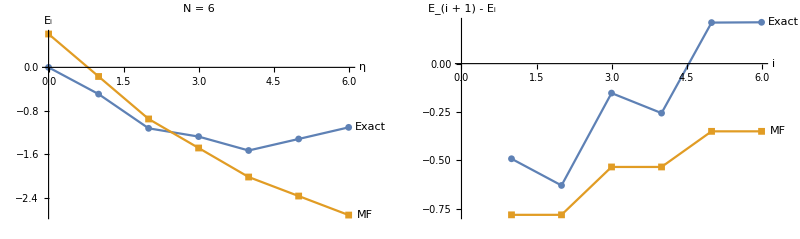

```mathematica
GraphicsGrid[{{energiesPlot, differencesPlot}}]
```

## Occupancy number

```mathematica
(*Occupancy number operators; for each energy level and for the total occupancy*)
Nop[i_] := nc[c[CR, i,  UP],c[AN, i, UP]] + nc[c[CR, i,  DO],c[AN, i, DO]];
NopTotal:=Sum[Nop[i],{i,n}];
```

```mathematica
(*Occupancy number functions; calculate the expected occupancy of a given state*)
Nlevels[state_]:=Table[scalarproductvc[state,ap[Nop[i],state]],{i, n}];
Ntotal[state_]:=scalarproductvc[state,ap[NopTotal,state]];
```

```mathematica
OccupancyTotalTable = Table[Ntotal[η[[i]]],{i, n+1}]
```

{5,4.02613,3.0755,2.19711,2.7195,2.19711}

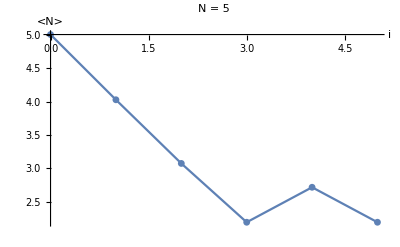

```mathematica
occupancyPlot=ListPlot[OccupancyTotalTable, DataRange->{0,n},
Joined->True,PlotMarkers->{Automatic,7},AxesOrigin->{0,n},AxesLabel->{"i","<N>"},
PlotLabel->"N = "<>ToString[n]]
```

```mathematica
d[n]
```

0.-0.488679 c_(2⇑)^†+0.872464 c_(2↓)^

```mathematica
Table[d[i],{i,n}]
```

{0.-0.114298 c_(5⇑)^†+0.993447 c_(5↓)^,0.-0.157125 c_(4⇑)^†+0.987579 c_(4↓)^,0.-0.246586 c_(3⇑)^†+0.969121 c_(3↓)^,0.+0.872464 c_(1⇑)^†-0.488679 c_(1↓)^,0.-0.488679 c_(2⇑)^†+0.872464 c_(2↓)^}

## Multiple n

```mathematica
(*These are lists of occupancy number during iteration (output of OccupancyTotalTable), copied and pasted for different n and for μ=0.*)
```

```mathematica
occ5={5,5.8967722406307175,5.,5.711769138634903,4.999999999999999,5.};
occ6={6,6.912576507711878,6.,6.801229903316978,6.,6.4075912151776535,6.000000000000002};
occ7={7,7.922170218996732,7.,7.8464187123465905,7.,7.622177329265054,7.000000000000002,7.000000000000003};
occ8={8,8.92895750827062,7.9999999999999964,8.873288499433102,7.9999999999999964,8.732335456112619,7.999999999999995,8.337461058080615,7.9999999999999964};
occ9={9,9.933833325938792,9.,9.890569142555966,8.999999999999998,9.793820582992632,8.999999999999996,9.546547345201734,8.999999999999996,8.999999999999996};
occ10={10,10.937564831293612,10.,10.902589203299108,10.000000000000004,10.831634204225551,10.000000000000002,10.66836440613069,10.000000000000004,10.286920068788051,10.000000000000002};
occ11={11,11.940477082834816,11.000000000000004,11.911337954170323,11.000000000000007,11.856630866125283,11.000000000000012,11.74203214885691,11.00000000000001,11.484237510795964,11.000000000000012,11.000000000000014}
```

{11,11.9405,11.,11.9113,11.,11.8566,11.,11.742,11.,11.4842,11.,11.}

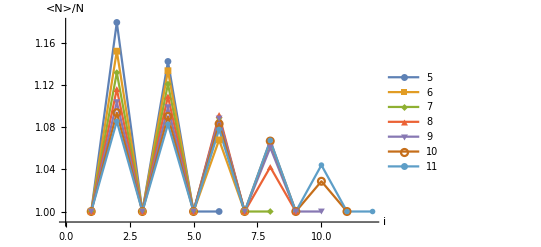

```mathematica
occupancyPlot=ListPlot[
{occ5/5,
occ6/6,
occ7/7,
occ8/8,
occ9/9,
occ10/10,
occ11/11},
PlotLegends->{5,6,7,8,9,10,11},
Joined->True,PlotMarkers->{Automatic,7},AxesLabel->{"i","<N>/N"}]
```

```mathematica
(*Export["occupancy_many_n.pdf", occupancyPlot];*)
```